# TransformedDistribution

```mathematica
D1=NormalDistribution[0,1]
```

NormalDistribution[0,1]

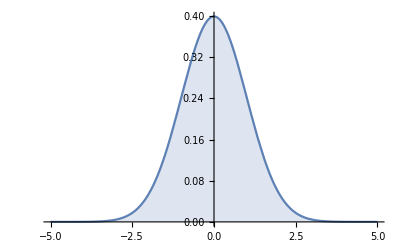

```mathematica
Plot[PDF[D1,x],{x,-5,5},Filling-> Axis,PlotRange-> All]
```

```mathematica
D2=TransformedDistribution[x^2,x\[Distributed]NormalDistribution[0,1]]
```

ChiSquareDistribution[1]

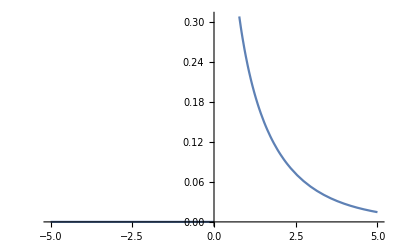

```mathematica
Plot[PDF[D2,x],{x,-5,5}]
```